```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/linear-stability

```mathematica
Get["../../neupackage/mma/fourier-mode-growth.wl"]
```

Parameters

```mathematica
dim=10
```

10

```mathematica
matRegular[11,2 ,0.1]//MatrixForm
```

(-10 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.1 | -8 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.1 | -6 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.1 | -4 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.1 | -2 | 0.1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.1 | 0 | 0.1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.1 | 2 | 0.1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 4 | 0.1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 6 | 0.1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 8 | 0.1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 10)

```mathematica
eigenSys[21,1,0.1][[1]]
```

{-10.01,-9.00005,-8.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,-1.42109×10^-14,1.,2.,3.,4.,5.,6.,7.,8.,9.00005,10.01}

```mathematica
matRegular2[dim,2 ,{0.5,0.1}]//MatrixForm
```

(-8 | 0.5 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5 | -6 | 0.5 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0
0.1 | 0.5 | -4 | 0.5 | 0.1 | 0 | 0 | 0 | 0 | 0
0 | 0.1 | 0.5 | -2 | 0.5 | 0.1 | 0 | 0 | 0 | 0
0 | 0 | 0.1 | 0.5 | 0 | 0.5 | 0.1 | 0 | 0 | 0
0 | 0 | 0 | 0.1 | 0.5 | 2 | 0.5 | 0.1 | 0 | 0
0 | 0 | 0 | 0 | 0.1 | 0.5 | 4 | 0.5 | 0.1 | 0
0 | 0 | 0 | 0 | 0 | 0.1 | 0.5 | 6 | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 0.5 | 8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
matRegularZeroDiag[dim,2 ,{0.5,0.1}]//MatrixForm
```

(0 | {0.5,0.1} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
{0.5,0.1} | 0 | {0.5,0.1} | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | {0.5,0.1} | 0 | {0.5,0.1} | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | {0.5,0.1} | 0 | {0.5,0.1} | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | {0.5,0.1} | 0 | {0.5,0.1} | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | {0.5,0.1} | 0 | {0.5,0.1} | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | {0.5,0.1} | 0 | {0.5,0.1} | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | {0.5,0.1} | 0 | {0.5,0.1} | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | {0.5,0.1} | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

Calculation

```mathematica
matRegular[dim,2 ,0.1]//MatrixForm
```

(-8 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.1 | -6 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.1 | -4 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.1 | -2 | 0.1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.1 | 0 | 0.1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.1 | 2 | 0.1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.1 | 4 | 0.1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 6 | 0.1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
eigenSys[dim,1,0.1][[2,{1,2,3}]]
```

{{0.995074,-0.0990155,0.00493443,-0.000164073,4.09369×10^-6,-8.17384×10^-8,1.36037×10^-9,-1.94098×10^-11,2.42321×10^-13,0.},{0.0990135,0.990086,-0.099502,0.00498329,-0.000166246,4.15817×10^-6,-8.31903×10^-8,1.38682×10^-9,-1.98116×10^-11,0.},{0.004975,0.0995,0.990025,-0.0995008,0.00498335,-0.00016625,4.15834×10^-6,-8.31945×10^-8,1.38658×10^-9,0.}}

```mathematica
eigenSys[dim,1,0][[2]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

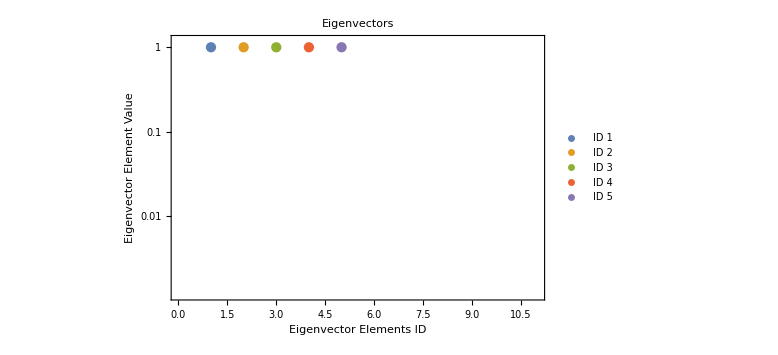

```mathematica
eigenVectorPlot[eigenSys[dim,1,0][[2]],{1,2,3,4,5},{{0,dim+1},{0,1.2}}]
```

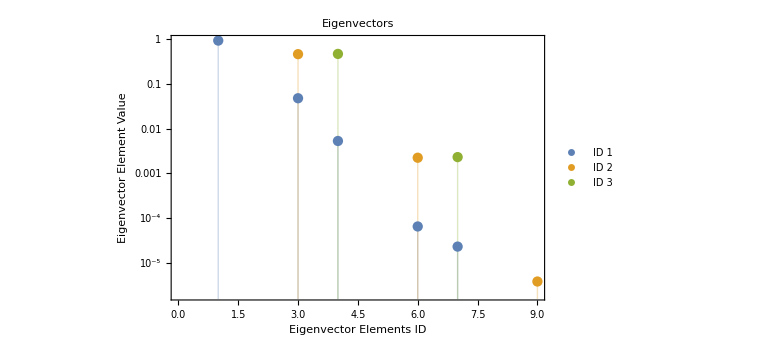

```mathematica
eigenVectorPlot2[eigenSys2[dim,1,{0.5,0.1}][[2]],{1,2,3},Automatic]
```

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Dot::dotsh: Tensors {Fit[{-2.31248,-5.31152,-8.7152,-12.4061,-16.3197,-20.4155,-24.6652,-29.0485,Indeterminate},{1,x},x]} and {1,0.000224714} have incompatible shapes.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of Fit::fitm will be suppressed during this calculation.

Dot::dotsh: Tensors {Fit[{-2.31248,-5.31152,-8.7152,-12.4061,-16.3197,-20.4155,-24.6652,-29.0485,Indeterminate},{1.,x},x]} and {1.,0.000224714} have incompatible shapes.

Dot::dotsh: Tensors {Fit[{-2.31248,-5.31152,-8.7152,-12.4061,-16.3197,-20.4155,-24.6652,-29.0485,Indeterminate},{1,x},x]} and {1,0.224715} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

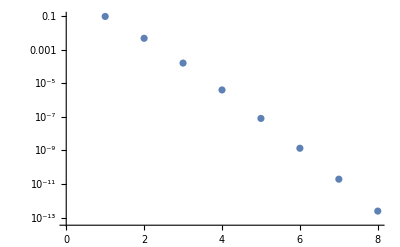

```mathematica
Show[
ListLogPlot[
Abs@eigenSys[dim,1,0.1][[2,1,2;;]]
]
,
Plot[
eigenVecSlopeFit[
eigenSys[dim,1,0.1][[2,1,2;;]] 
].{1,y},
{y,0,dim+1}
]

]
```

```mathematica
evRatioSlope=Table[

{odrat,eigenVecSlopeFit[
eigenSys[dim,1,1/odrat][[2,1,2;;]] 
][[2]]},

{odrat,1,100}
];
```

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Part::partw: Part 2 of {Fit[{Log[-4-100 Root[«1»&,1,0]+88 Root[«3»]^2+76 Root[«3»]^3-65 Root[«3»]^4-Root[«3»]^5+7 Root[«3»]^6-Root[«3»]^7],Log[11+36 Root[«1»&,1,0]-75 Root[«3»]^2+15 Root[«3»]^3+20 Root[«3»]^4-9 Root[«3»]^5+Root[«1»&,1,0]^6],Log[-18+17 Root[«1»&,1,0]+26 Root[«3»]^2-31 Root[«3»]^3+10 Root[«3»]^4-Root[«3»]^5],«3»,Log[4-Root[«1»&,1,0]],0,-∞},{1,x},x]} does not exist.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Part::partw: Part 2 of {Fit[{Log[-8-3724 Root[«1»&,1,0]+1196 Root[«3»]^2+1006 Root[«3»]^3-340 Root[«3»]^4-22 Root[«3»]^5+14 Root[«3»]^6-Root[«3»]^7],Log[47+972 Root[«1»&,1,0]-630 Root[«3»]^2-60 Root[«3»]^3+95 Root[«3»]^4-18 Root[«3»]^5+Root[«1»&,1,0]^6],Log[-180-211 Root[«1»&,1,0]+352 Root[«3»]^2-136 Root[«3»]^3+20 Root[«3»]^4-Root[«3»]^5],«3»,Log[8-Root[«1»&,1,0]],0,-∞},{«1»},x]} does not exist.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of Fit::fitm will be suppressed during this calculation.

Part::partw: Part 2 of {Fit[{Log[-12-38084 Root[«1»&,1,0]+7704 Root[«3»]^2+4796 Root[«3»]^3-1035 Root[«3»]^4-57 Root[«3»]^5+21 Root[«3»]^6-Root[«3»]^7],Log[107+6588 Root[«1»&,1,0]-2595 Root[«3»]^2-315 Root[«3»]^3+220 Root[«3»]^4-27 Root[«3»]^5+Root[«1»&,1,0]^6],«5»,0,-∞},{1,x},x]} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

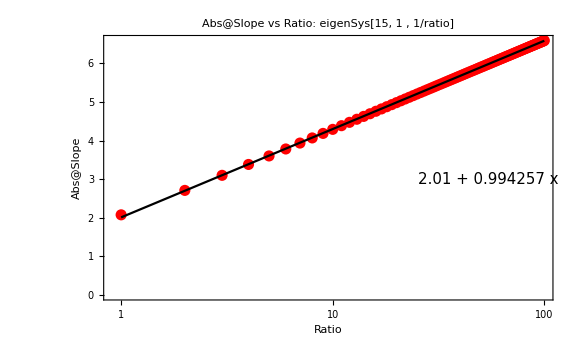

```mathematica
Show[
ListLogLinearPlot[
Abs@evRatioSlope[[1;;]],Frame->True,FrameLabel->{"Ratio","Abs@Slope"},ImageSize->Large,PlotLabel->"Abs@Slope vs Ratio: eigenSys["<>ToString@dim<>", 1 , 1/ratio]",Epilog->Inset[Style[
ToString@Fit[
{N@Log@#[[1]],#[[2]]}&/@(Abs@evRatioSlope[[1;;]]),
{1,x},x
]
,15],{4,3}],PlotStyle->Red
]
,
LogLinearPlot[
CoefficientList[
Fit[
{N@Log@#[[1]],#[[2]]}&/@(Abs@evRatioSlope[[1;;]]),
{1,z},z
],z
].{1,Log@y},
{y,1,100},Frame->True,ImageSize->Large,PlotStyle->Black
]

]
```

## Time Evolution

```mathematica
eigenSys[dim,1,0.1][[1]]//Length
matRegular[dim,1 ,0.1]
```

15

{{-7,0.1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.1,-6,0.1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.1,-5,0.1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0.1,-4,0.1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0.1,-3,0.1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0.1,-2,0.1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0.1,-1,0.1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0.1,0,0.1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0.1,1,0.1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0.1,2,0.1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0.1,3,0.1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0.1,4,0.1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0.1,5,0.1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0.1,6,0.1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0.1,7}}

```mathematica
eigensystemT=eigenSys[dim,1,0.1];
initEigen=eigensystemT[[2,(dim-1)/2]]
init=ReplacePart[Table[0,{i,1,dim}],Floor[dim/2]->10^(-3)]
init2=ReplacePart[Table[0,{i,1,dim}],{Floor[dim/2]->10^(-3),Floor[dim/2]+1->10^(-3)}]
init3=Table[1/dim,{i,1,dim}]
```

{1.38658×10^-9,8.31945×10^-8,4.15834×10^-6,0.00016625,0.00498335,0.0995008,0.990025,-0.0995008,0.00498335,-0.00016625,4.15834×10^-6,-8.31945×10^-8,1.38691×10^-9,-1.98165×10^-11,2.47706×10^-13}

{0,0,0,0,0,0,1/1000,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,1/1000,1/1000,0,0,0,0,0,0,0}

{1/15,1/15,1/15,1/15,1/15,1/15,1/15,1/15,1/15,1/15,1/15,1/15,1/15,1/15,1/15}

```mathematica
eqn=I D[waveFun[dim,x],x]==matRegular[dim,1,0.1].waveFun[dim,x]&&waveFun[dim,0]==initEigen//Quiet
```

{ⅈ epsilon1'[x],ⅈ epsilon2'[x],ⅈ epsilon3'[x],ⅈ epsilon4'[x],ⅈ epsilon5'[x],ⅈ epsilon6'[x],ⅈ epsilon7'[x],ⅈ epsilon8'[x],ⅈ epsilon9'[x],ⅈ epsilon10'[x],ⅈ epsilon11'[x],ⅈ epsilon12'[x],ⅈ epsilon13'[x],ⅈ epsilon14'[x],ⅈ epsilon15'[x]}=={-7 epsilon1[x]+0.1 epsilon2[x],0.1 epsilon1[x]-6 epsilon2[x]+0.1 epsilon3[x],0.1 epsilon2[x]-5 epsilon3[x]+0.1 epsilon4[x],0.1 epsilon3[x]-4 epsilon4[x]+0.1 epsilon5[x],0.1 epsilon4[x]-3 epsilon5[x]+0.1 epsilon6[x],0.1 epsilon5[x]-2 epsilon6[x]+0.1 epsilon7[x],0.1 epsilon6[x]-epsilon7[x]+0.1 epsilon8[x],0.1 epsilon7[x]+0.1 epsilon9[x],0.1 epsilon10[x]+0.1 epsilon8[x]+epsilon9[x],2 epsilon10[x]+0.1 epsilon11[x]+0.1 epsilon9[x],0.1 epsilon10[x]+3 epsilon11[x]+0.1 epsilon12[x],0.1 epsilon11[x]+4 epsilon12[x]+0.1 epsilon13[x],0.1 epsilon12[x]+5 epsilon13[x]+0.1 epsilon14[x],0.1 epsilon13[x]+6 epsilon14[x]+0.1 epsilon15[x],0.1 epsilon14[x]+7 epsilon15[x]}&&{epsilon1[0],epsilon2[0],epsilon3[0],epsilon4[0],epsilon5[0],epsilon6[0],epsilon7[0],epsilon8[0],epsilon9[0],epsilon10[0],epsilon11[0],epsilon12[0],epsilon13[0],epsilon14[0],epsilon15[0]}=={1.38658×10^-9,8.31945×10^-8,4.15834×10^-6,0.00016625,0.00498335,0.0995008,0.990025,-0.0995008,0.00498335,-0.00016625,4.15834×10^-6,-8.31945×10^-8,1.38691×10^-9,-1.98165×10^-11,2.47706×10^-13}

```mathematica
sol=NDSolve[eqn,waveFun[dim,x],{x,0,20}];
```

```mathematica
wf[x_]=waveFun[dim,x]/.First@sol;
```

```mathematica
wf[0.1]
```

{1.37965×10^-9+1.38427×10^-10 ⅈ,8.27789×10^-8+8.30559×10^-9 ⅈ,4.13757×10^-6+4.15141×10^-7 ⅈ,0.00016542+0.0000165973 ⅈ,0.00495846+0.000497505 ⅈ,0.0990037+0.00993351 ⅈ,0.985079+0.0988376 ⅈ,-0.0990037-0.00993351 ⅈ,0.00495846+0.000497505 ⅈ,-0.00016542-0.0000165973 ⅈ,4.13757×10^-6+4.15141×10^-7 ⅈ,-8.27789×10^-8-8.3056×10^-9 ⅈ,1.37998×10^-9+1.3846×10^-10 ⅈ,-1.97175×10^-11-1.97835×10^-12 ⅈ,2.46468×10^-13+2.47293×10^-14 ⅈ}

```mathematica
ListAnimate[
Table[ListLogPlot[Abs@wf[t],PlotRange->{{0,dim},{10^(-24),1}}],{t,0,20,0.1}]
]
```

```mathematica
Export["fourier-modes-all-1-initial-time-evo.mov",Out[221],"VideoEncoding"->"MPEG-4 Video"]
```

Export::infer: Cannot infer format of file "fourier-modes-all-1-initial-time-evo.mp4".

$Failed

```mathematica
coeff[n_]:=Module[{funListM},

funListM=Table[Symbol["a"<>ToString@i],{i,1,n}];

funListM

]
```

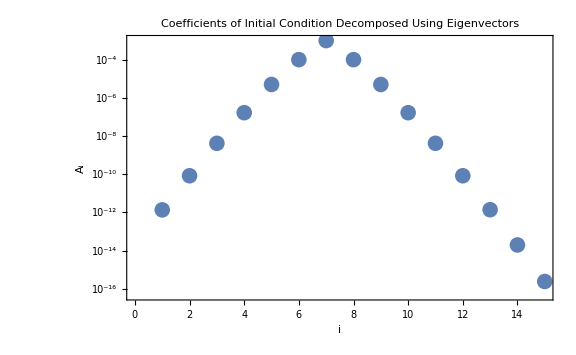

```mathematica
ListLogPlot[
Abs[coeff[dim]]/.First@NSolve[coeff[dim].eigenSys[dim,1,0.1][[2]]==init,coeff[dim]],
Frame->True,FrameLabel->{"i","A_i"},ImageSize->Large,PlotLabel->"Coefficients of Initial Condition Decomposed Using Eigenvectors"
]
```

I can plot out the time evolution using this

```mathematica
timeEVO[t_]=(Exp[-I # t]&/@eigensystemT[[1]]);
timeCOEFF=(coeff[dim]/.First@NSolve[coeff[dim].eigenSys[dim,1,0.1][[2]]==init,coeff[dim]]);
timeEIGEN=eigenSys[dim,1,0.1][[2]];
```

```mathematica
theoryElement[t_]=Table[
timeEVO[t][[i]]*timeCOEFF[[i]],
{i,1,dim}
].(eigenSys[dim,1,0.1][[2]]);
```

```mathematica
Abs@theoryElement[1]
```

{1.0781×10^-12,6.74387×10^-11,3.51556×10^-9,1.4659×10^-7,4.5829×10^-6,0.000095445,0.000990827,0.000095445,4.5829×10^-6,1.4659×10^-7,3.51556×10^-9,6.74387×10^-11,1.07796×10^-12,1.47682×10^-14,1.77042×10^-16}

```mathematica
ListAnimate[
Table[ListLogPlot[{Abs@theoryElement[t],Abs@wf[t]},PlotRange->{{0,dim+1},{10^(-24),1}},PlotMarkers->{{"+",11},{"○",10}},Frame->True,ImageSize->Large,PlotLegends->Placed[{"Theory","Numerical"},{Right,Top}],PlotLabel->"Analytical and Numerical Comparison",Epilog->Inset[Style["Time: "<>ToString@t,15],{1,-2},{Left,Top}] 
],{t,0,20,0.1}]
]
```

$Aborted

```mathematica
Export["compare-theory-numerical.mov",Out[165]]
```

compare-theory-numerical.mov

```mathematica
(a Sin[b t]+c Cos[d t])/.FindFit[
Table[
Abs@theoryElement[t][[1]],
{t,0,5,0.1}
],
a Sin[b t]+c Cos[d t],
{a,b,c,d},
t
]
```

-2.52356×10^-13 Cos[0.96332 t]+2.40813×10^-13 Sin[1.03377 t]

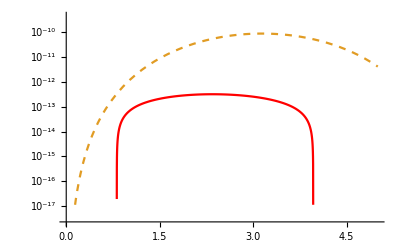

```mathematica
LogPlot[{-2.523555246017889*^-13 Cos[0.9633202397411789 t]+2.4081257283745396*^-13 Sin[1.0337728193171671 t],Abs@theoryElement[t][[1]]},{t,0,5},PlotStyle->{Red,Dashed}]
```

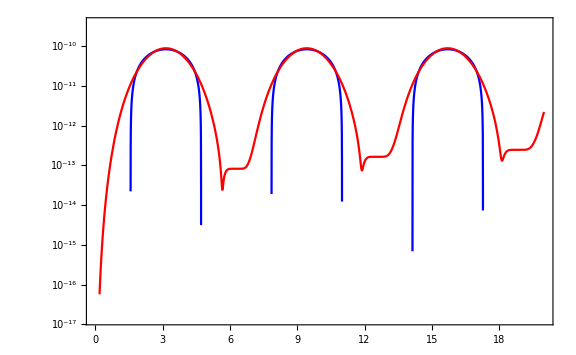

```mathematica
LogPlot[{timeCOEFF[[2]] Cos[eigenSys[dim,1,0.1][[1,6]]t/2],Abs@theoryElement[t][[1]]},{t,0,20},PlotStyle->{Blue,Red},Frame->True,ImageSize->Large]
```

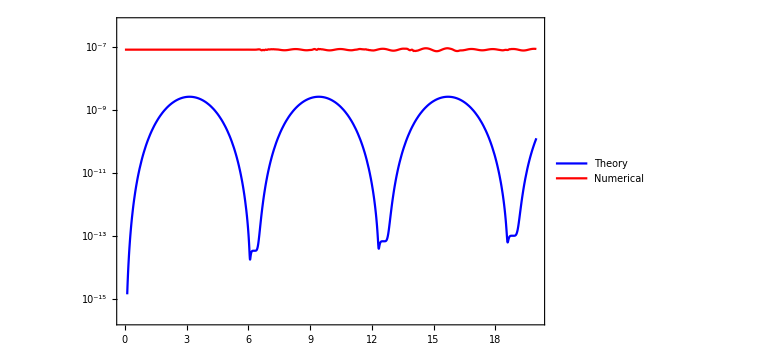

```mathematica
LogPlot[{Abs@theoryElement[t][[2]],Abs@wf[t][[2]]},{t,0,20},PlotStyle->{Blue,Red},Frame->True,ImageSize->Large,PlotLegends->{"Theory","Numerical"}]
```

```mathematica
h[m_,t_,alpha_]:=Exp[-I m t]Exp[-alpha m]Exp[0.1(Exp[-I t]Exp[-alpha]-Exp[I t]Exp[alpha])]
```

```mathematica
Abs[h[1,2,10]]
```

5.52046803863236×10^393

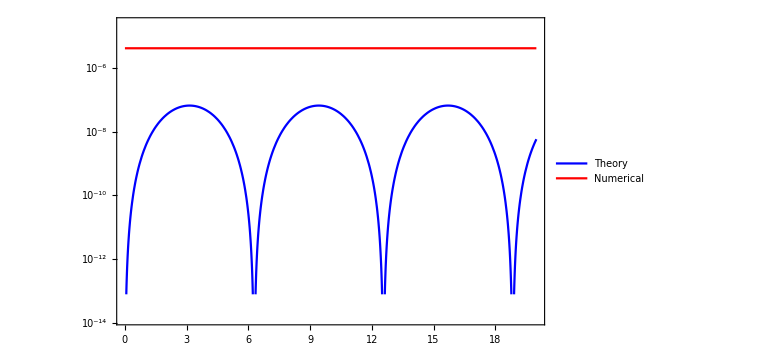

```mathematica
LogPlot[{Abs@theoryElement[t][[3]],Abs@wf[t][[3]]},{t,0,20},PlotStyle->{Blue,Red},Frame->True,ImageSize->Large,PlotLegends->{"Theory","Numerical"}]
```

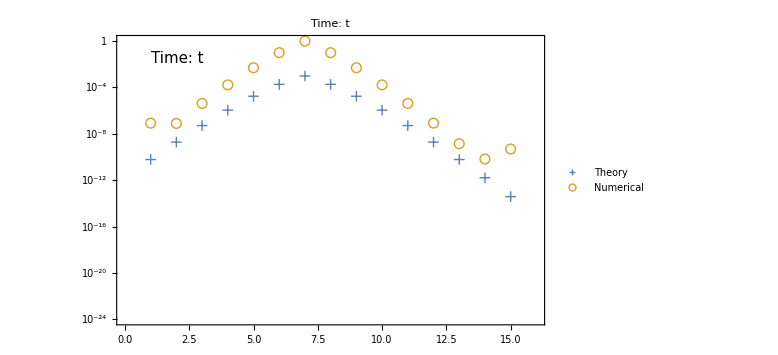

```mathematica
ListLogPlot[{Abs@theoryElement[t],Abs@wf[t]}/.t->15,PlotRange->{{0,dim+1},{10^(-24),1}},PlotMarkers->{{"+",11},{"○",10}},Frame->True,ImageSize->Large,PlotLegends->Placed[{"Theory","Numerical"},{Right,Top}],PlotLabel->"Time: "<>ToString[t],Epilog->Inset[Style["Time: "<>ToString@t,15],{1,-2},{Left,Top}]]
```

```mathematica
(Sin[# t]&/@eigensystemT[[1]]).(Abs[coeff[dim]]/.First@NSolve[coeff[dim].eigenSys[dim,1,0.1][[2]]==init,coeff[dim]])
```

0.0000995008 Sin[7.99361×10^-15 t]-0.000990025 Sin[1. t]+4.98335×10^-6 Sin[1. t]-0.0000995008 Sin[2. t]+1.6625×10^-7 Sin[2. t]+4.15834×10^-9 Sin[3. t]-4.98335×10^-6 Sin[3. t]-1.66167×10^-7 Sin[4. t]-4.15834×10^-9 Sin[5. t]+1.38691×10^-12 Sin[5. t]-8.31903×10^-11 Sin[6.00005 t]+1.98152×10^-14 Sin[6.00005 t]+2.42354×10^-16 Sin[7.00995 t]-1.36037×10^-12 Sin[7.00995 t]

### Zero Diag

```mathematica
matRegularZeroDiag[dim,1,0.1]//MatrixForm
```

(0 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.1 | 0 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.1 | 0 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.1 | 0 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.1 | 0 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.1 | 0 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.1 | 0 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 0 | 0.1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 0 | 0.1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 0 | 0.1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 0 | 0.1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 0 | 0.1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 0 | 0.1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 0 | 0.1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.1 | 0)

```mathematica
Eigensystem[
matRegularZeroDiag[dim,1,0.1]
][[1,dim]]
```

8.32667×10^-17

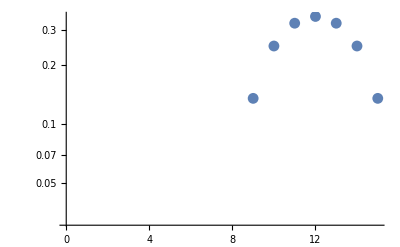

```mathematica
ListLogPlot@Eigensystem[
matRegularZeroDiag[dim,1,0.1]
][[2,3]]
```

```mathematica
eqnZeroDiag=I D[waveFun[dim,x],x]==matRegularZeroDiag[dim,1,0.1].waveFun[dim,x]&&waveFun[dim,0]==init//Quiet
```

{ⅈ epsilon1'[x],ⅈ epsilon2'[x],ⅈ epsilon3'[x],ⅈ epsilon4'[x],ⅈ epsilon5'[x],ⅈ epsilon6'[x],ⅈ epsilon7'[x],ⅈ epsilon8'[x],ⅈ epsilon9'[x],ⅈ epsilon10'[x],ⅈ epsilon11'[x],ⅈ epsilon12'[x],ⅈ epsilon13'[x],ⅈ epsilon14'[x],ⅈ epsilon15'[x]}=={0.1 epsilon2[x],0.1 epsilon1[x]+0.1 epsilon3[x],0.1 epsilon2[x]+0.1 epsilon4[x],0.1 epsilon3[x]+0.1 epsilon5[x],0.1 epsilon4[x]+0.1 epsilon6[x],0.1 epsilon5[x]+0.1 epsilon7[x],0.1 epsilon6[x]+0.1 epsilon8[x],0.1 epsilon7[x]+0.1 epsilon9[x],0.1 epsilon10[x]+0.1 epsilon8[x],0.1 epsilon11[x]+0.1 epsilon9[x],0.1 epsilon10[x]+0.1 epsilon12[x],0.1 epsilon11[x]+0.1 epsilon13[x],0.1 epsilon12[x]+0.1 epsilon14[x],0.1 epsilon13[x]+0.1 epsilon15[x],0.1 epsilon14[x]}&&{epsilon1[0],epsilon2[0],epsilon3[0],epsilon4[0],epsilon5[0],epsilon6[0],epsilon7[0],epsilon8[0],epsilon9[0],epsilon10[0],epsilon11[0],epsilon12[0],epsilon13[0],epsilon14[0],epsilon15[0]}=={0,0,0,0,0,0,1/1000,0,0,0,0,0,0,0,0}

```mathematica
Eigensystem[matRegularZeroDiag[dim,2 ,0.1]][[1]]
```

{0.196157,-0.196157,0.184776,-0.184776,0.166294,-0.166294,0.141421,-0.141421,0.111114,-0.111114,0.0765367,-0.0765367,0.0390181,-0.0390181,8.32667×10^-17}

```mathematica
solZeroDiag=NDSolve[eqnZeroDiag,waveFun[dim,x],{x,0,20}];
```

```mathematica
wfZeroDiag[x_]=waveFun[dim,x]/.First@solZeroDiag;
```

```mathematica
ListAnimate[
Table[ListLogPlot[Abs@wfZeroDiag[t],PlotRange->{{0,dim+1},{10^(-24),1}}],{t,0,30,0.1}]
]
```

## Change of Slope Increasing Rate due to dimension

```mathematica
ss[dimension_]:=Module[{evRatioSlopeM},

evRatioSlopeM=Table[

{odrat,eigenVecSlopeFit[
eigenSys[dimension,1,1/odrat][[2,1,2;;]] 
][[2]]},

{odrat,1,10}
];


Coefficient[
Fit[
{N@Log@#[[1]],#[[2]]}&/@(Abs@evRatioSlopeM[[1;;]]),
{1,z},z
],z
]

]
```

```mathematica
Table[
ss[dimension],
{dimension,11,21,2}
]
```

{0.960123,0.964271,0.967577,0.970288,0.972557,0.974488}

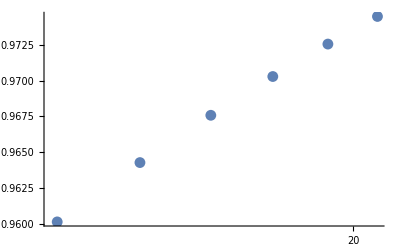

```mathematica
ListLogLinearPlot[
Transpose@Join[{Table[i,{i,11,21,2}]},{Out[62]}]
]
```

```mathematica
ss1[dimension_]:=Module[{evRatioSlopeM},

evRatioSlopeM=Table[

{odrat,eigenVecSlopeFit[
eigenSys[dimension,1,1/odrat][[2,1,2;;]] 
][[2]]},

{odrat,1,10}
];


Coefficient[
Fit[
{N@Log@#[[1]],#[[2]]}&/@(Abs@evRatioSlopeM[[1;;]]),
{1,z},z
],z
][[1]]

]
```

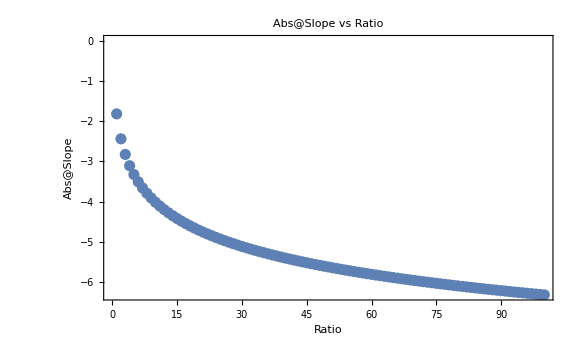

```mathematica
ListPlot[
evRatioSlope,Frame->True,FrameLabel->{"Ratio","Abs@Slope"},ImageSize->Large,PlotLabel->"Abs@Slope vs Ratio"
]
```

## More Offdiag Elements

```mathematica
evRatioSlope2=Table[

{odrat,eigenVecSlopeFit2[
eigenSys2[dim,1,{1,1}/odrat][[2,1,2;;]] 
][[2]]},

{odrat,1,100}
];
```

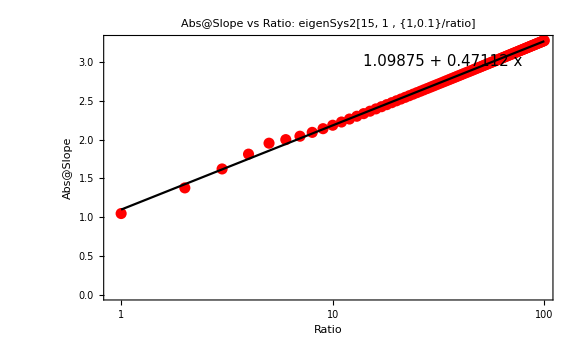

```mathematica
Show[
ListLogLinearPlot[
Abs@evRatioSlope2[[1;;]],Frame->True,FrameLabel->{"Ratio","Abs@Slope"},ImageSize->Large,PlotLabel->"Abs@Slope vs Ratio: eigenSys2["<>ToString@dim<>", 1 , {1,0.1}/ratio]",Epilog->Inset[Style[
ToString@Fit[
{N@Log@#[[1]],#[[2]]}&/@(Abs@evRatioSlope2[[1;;]]),
{1,x},x
]
,15],{3.5,3}],PlotStyle->Red
]
,
LogLinearPlot[
CoefficientList[
Fit[
{N@Log@#[[1]],#[[2]]}&/@(Abs@evRatioSlope2[[1;;]]),
{1,z},z
],z
].{1,Log@y},
{y,1,100},Frame->True,ImageSize->Large,PlotStyle->Black
]

]
```